```mathematica
dropboxDir="~/Dropbox/";
```

```mathematica
CI[boots_]:=Block[{LQ,UQ,upper,lower},
UQ=(1+Erf[1/Sqrt[2.]])/2;
LQ=(1-Erf[1/Sqrt[2.]])/2;
upper=Quantile[boots,UQ];
lower=Quantile[boots,LQ];
(upper-lower)/2];
```

```mathematica
Bin[data_,binsize_]:=Block[{newdata,L,newL},
L=Length[data];
newL=Floor[L/binsize];
newdata=ConstantArray[0,newL];
Do[Do[newdata[[i]]+=data[[(i-1)*binsize+k]]/binsize,{k,1,binsize}],{i,1,newL}];
newdata]
```

```mathematica
Nboot=200;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
gfmcLegend=PointLegend[{Directive[ColorData[97][14]],Directive[ColorData[97][15]]},{MaTeX["2/(\\alpha_s C)",Magnification->0.8],MaTeX["2/(\\alpha_V C)",Magnification->0.8]},LegendMarkers->{Graphics[Disk[]]},LegendLayout->{"Column",2},LegendMargins->0.5,LegendFunction->frame]
```

## α=0.2

```mathematica
α=0.2;
```

```mathematica
picDir=dropboxDir<>"/physics/projects/heavy_quark_nuclei/62d1dcb0570fab737342743d/figs/";
```

```mathematica
dataDir=dropboxDir<>"/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
bs=4;
```

```mathematica
dtau=0.4;
```

### LO meson

```mathematica
steps=1000;
walkers=5000;
V=4/3α
```

0.266667

```mathematica
NCoord=2;
```

```mathematica
(*dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

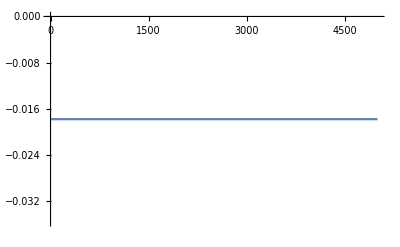

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

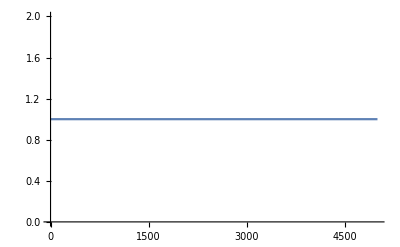

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

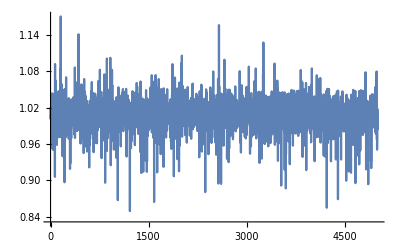

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

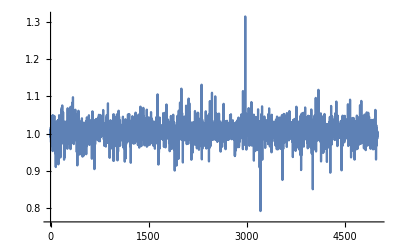

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

250

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

250

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{250,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.017777777777777780035

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.017777777777777780035

ListPlot::prng: Value of option PlotRange -> {-0.01866666666666666,-0.01600000000000000} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

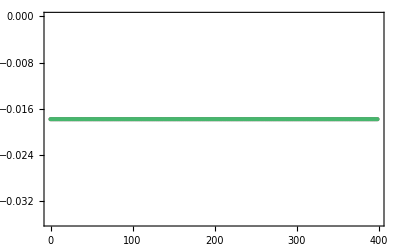

```mathematica
EMPQQbarLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.05ET,.9ET},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

```mathematica
EMPQQbarLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}],Frame->True,PlotRange->{1.00002ET,.99998ET}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

ListPlot::prng: Value of option PlotRange -> {-0.01777813333333333,-0.01777742222222222} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

```mathematica
Export[picDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarLO];
```

### NLO meson

```mathematica
steps=1000;
walkers=5000;
V=4/3α
```

0.266667

```mathematica
NCoord=2;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

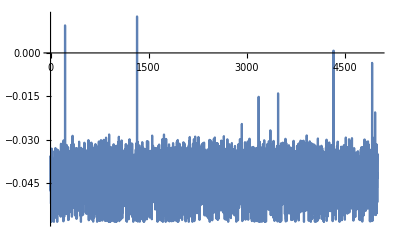

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

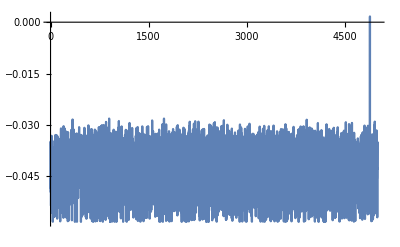

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

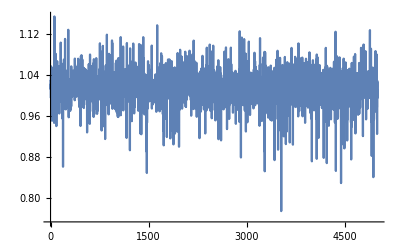

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

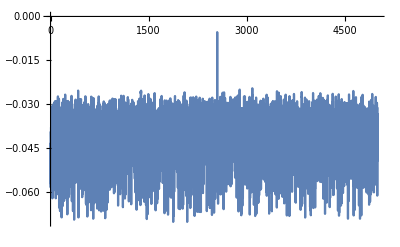

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

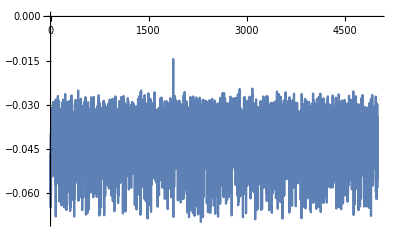

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

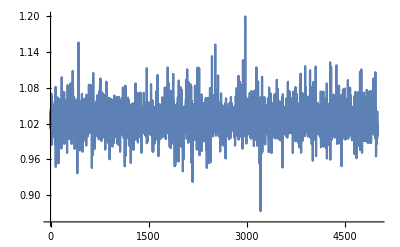

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

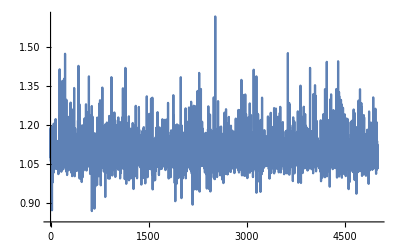

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

250

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

250

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{250,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.041020.00015

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.042280.00009

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

-0.043100.00016

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.csv"][[2,1]],Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.csv"][[2,2]]]
```

-0.043130.00004

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.0421839

```mathematica
EgfmcxxVec[[-1,1]]
```

398.4

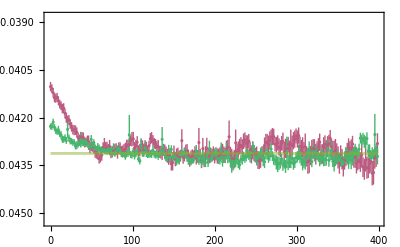

```mathematica
EMPQQbarNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.05Egfmc[[1]],.9Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.0000.004

```mathematica
(Evmc-ET)/Evmc
```

0.0480.005

```mathematica
(Egfmc-ET)/Egfmc
```

0.0490.004

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.01970.0024

```mathematica
(ETxx-ET)/ETxx
```

0.0300.004

### NNLO meson

```mathematica
steps=1000;
walkers=5000;
V=4/3α
```

0.266667

```mathematica
NCoord=2;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

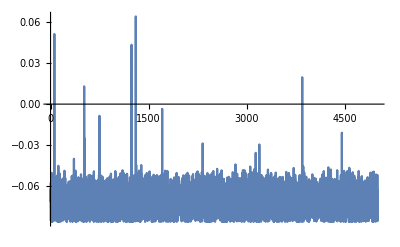

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

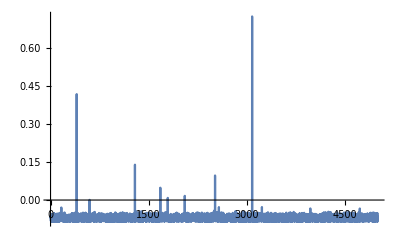

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

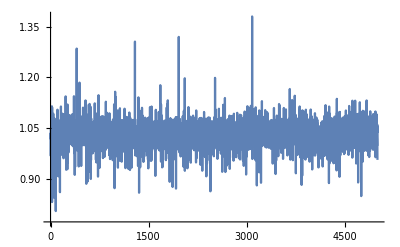

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

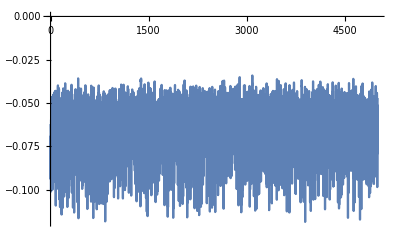

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

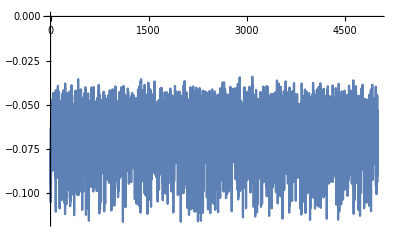

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

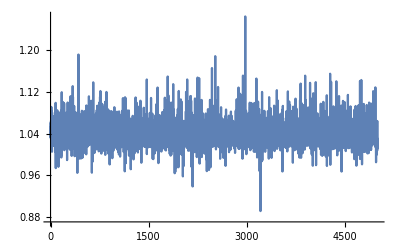

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

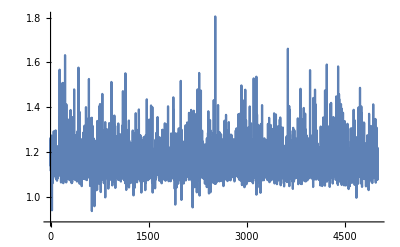

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

250

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

250

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{250,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.064970.00023

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.069530.00013

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

-0.07050.0004

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.csv"][[2,1]],Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.csv"][[2,2]]]
```

-0.070660.00010

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.0693996

```mathematica
EgfmcxxVec[[-1,1]]
```

398.4

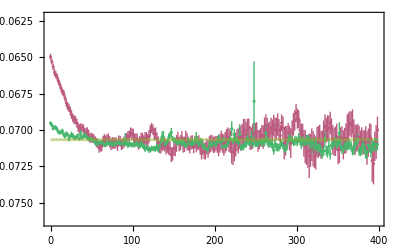

```mathematica
EMPQQbarNNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.08Egfmc[[1]],.88Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.0020.005

```mathematica
(Evmc-ET)/Evmc
```

0.0790.006

```mathematica
(Egfmc-ET)/Egfmc
```

0.08060.0035

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.01610.0023

```mathematica
(ETxx-ET)/ETxx
```

0.0660.004

### mNLO meson

```mathematica
steps=100;
walkers=50000;
V=4/3α
```

0.266667

```mathematica
NCoord=2;
```

```mathematica
dataBase=dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcxxHammys[[1,1]]
```

-0.0496125

```mathematica
gfmcxxHammys[[1,1]]
```

-0.0496125

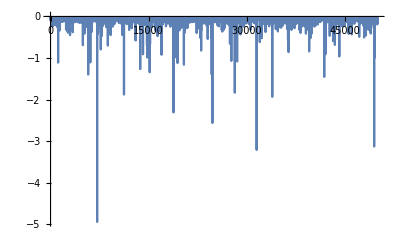

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

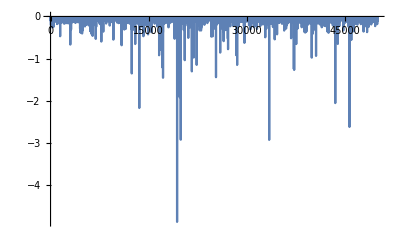

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

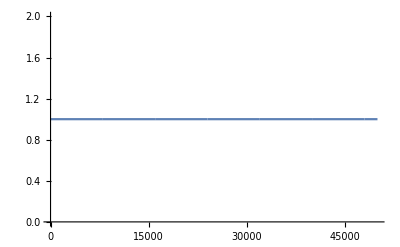

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

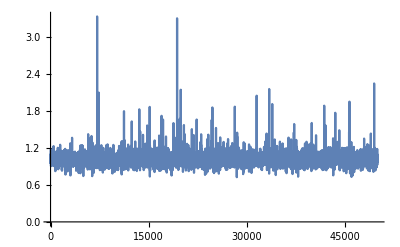

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

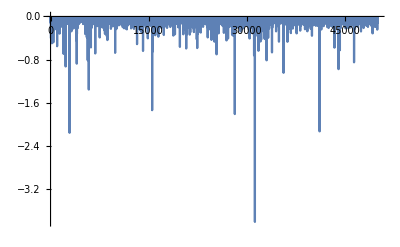

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

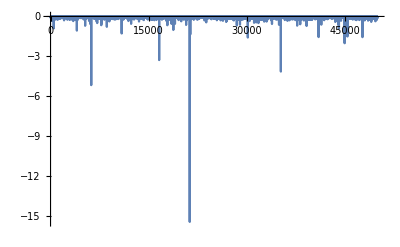

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

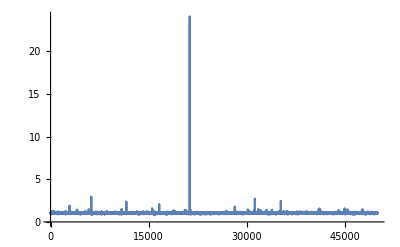

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

101

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

50000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

101

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

50000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

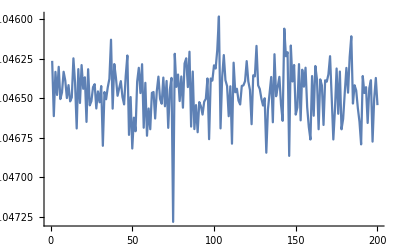

```mathematica
ListPlot[bootTab[[1]],Joined->True]
```

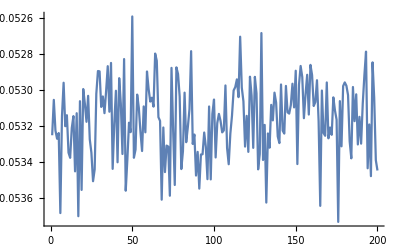

```mathematica
ListPlot[xxbootTab[[1]],Joined->True]
```

```mathematica
Dimensions[bootTab]
```

{101,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.046460.00017

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.053180.00021

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_ordermNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

-0.052490.00028

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,1]],Import[dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,2]]]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.4_Nstep100_Nwalkers50000_Ncoord2_Nc3_Nf4_alpha0.2_spoila1_spoilfhwf_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.4_Nstep100_Nwalkers50000_Ncoord2_Nc3_Nf4_alpha0.2_spoila1_spoilfhwf_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

$Failed⟦2,1⟧$Failed⟦2,2⟧

```mathematica
EMPQQbarmNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{{0,40},{2Evmc[[1]],.0Evmc[[1]]}},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{mNLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarmNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-0.1110.007

```mathematica
(Evmc-ET)/Evmc
```

0.1160.009

```mathematica
(Egfmc-ET)/Egfmc
```

0.0180.009

```mathematica
(Egfmc-ETxx)/Egfmc
```

-0.180.04

```mathematica
(ETxx-ET)/ETxx
```

0.160.04

### LO baryon

```mathematica
steps=1000;
walkers=5000;
V=4/3α/(3-1)
```

0.133333

```mathematica
NCoord=3;
```

```mathematica
(*dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

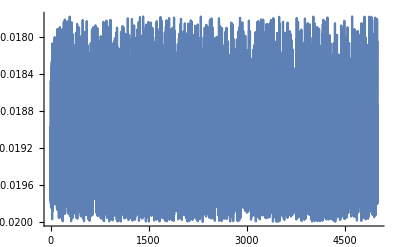

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

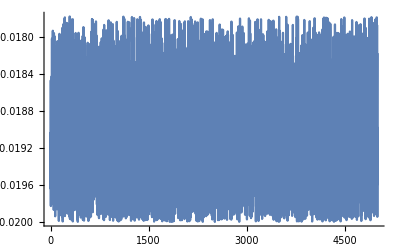

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

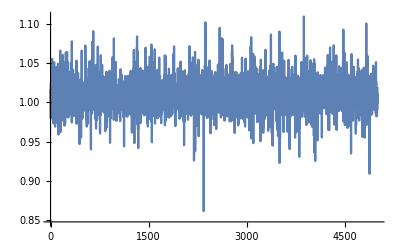

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

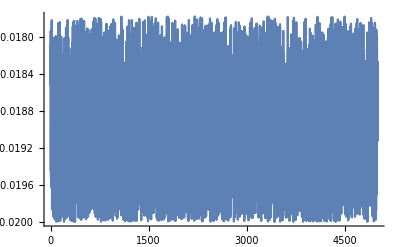

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

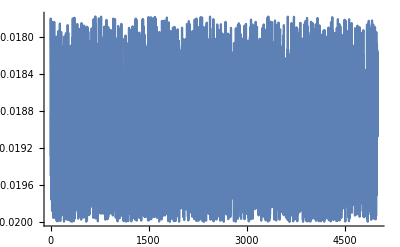

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

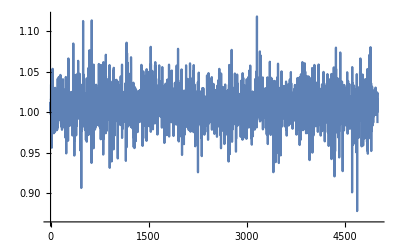

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

250

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

250

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{250,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.0190479

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.0190669

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

-0.0190299

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,1]],Import[dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,2]]]
```

-0.0190544

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.0190574

```mathematica
EgfmcxxVec[[-1,1]]
```

398.4

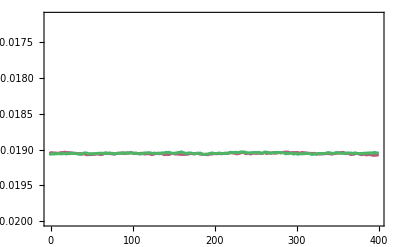

```mathematica
EMPQQbarLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.05Egfmc[[1]],.9Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

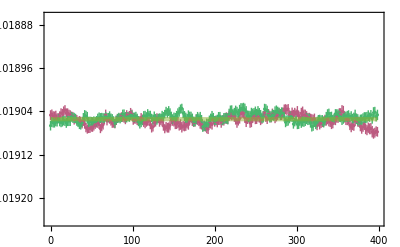

```mathematica
EMPQQbarLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.01Egfmc[[1]],.99Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.00130.0005

```mathematica
(Evmc-ET)/Evmc
```

-0.00090.0007

```mathematica
(Egfmc-ET)/Egfmc
```

0.00040.0005

```mathematica
(Egfmc-ETxx)/Egfmc
```

-0.00060.0005

```mathematica
(ETxx-ET)/ETxx
```

0.00100.0007

### NLO baryon

```mathematica
steps=1000;
walkers=5000;
V=4/3α/(3-1)
```

0.133333

```mathematica
NCoord=3;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.5.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

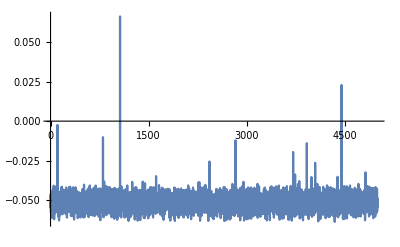

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

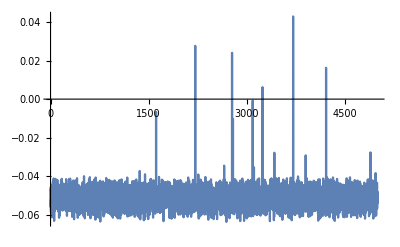

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

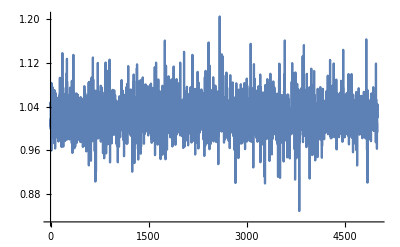

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

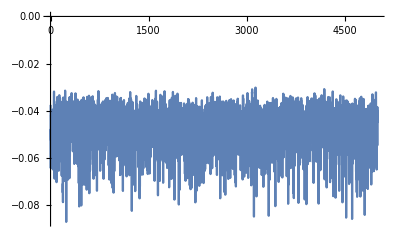

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

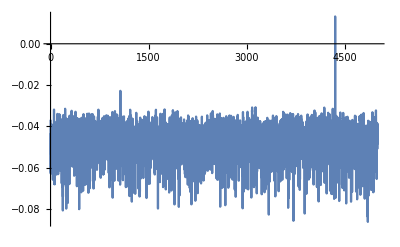

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

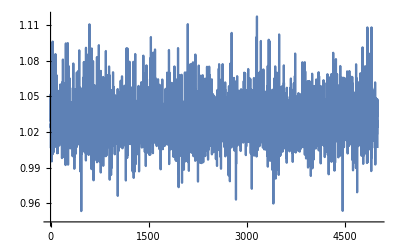

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

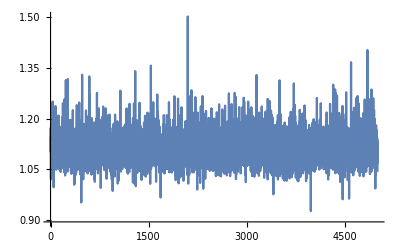

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

250

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

250

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{250,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.047480.00012

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.050510.00006

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

-0.051080.00010

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.5.csv"][[2,1]],Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.5.csv"][[2,2]]]
```

-0.051100.00005

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.0504435

```mathematica
EgfmcxxVec[[-1,1]]
```

398.4

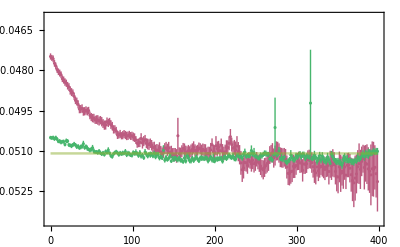

```mathematica
EMPQQbarNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.05Egfmc[[1]],.9Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.00030.0021

```mathematica
(Evmc-ET)/Evmc
```

0.07050.0030

```mathematica
(Egfmc-ET)/Egfmc
```

0.07080.0024

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.01150.0015

```mathematica
(ETxx-ET)/ETxx
```

0.05990.0026

### NNLO baryon

```mathematica
steps=1000;
walkers=5000;
V=4/3α/(3-1)
```

0.133333

```mathematica
NCoord=3;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.5.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

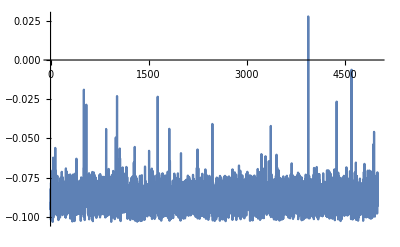

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

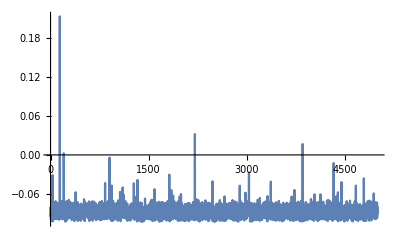

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

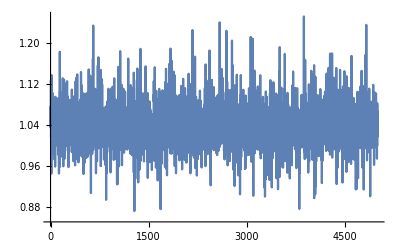

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

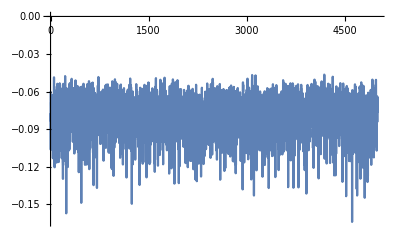

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

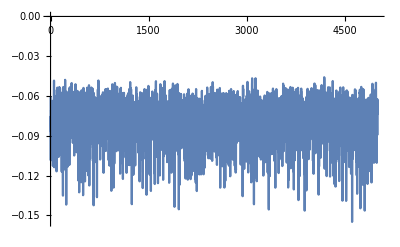

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

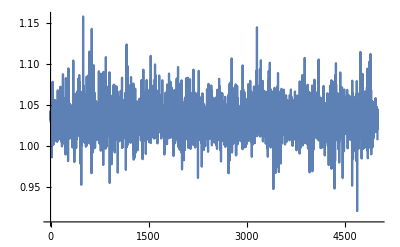

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

250

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

250

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{250,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.078240.00021

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.087420.00010

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

-0.087960.00019

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.5.csv"][[2,1]],Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.5.csv"][[2,2]]]
```

-0.088410.00011

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.0873186

```mathematica
EgfmcxxVec[[-1,1]]
```

398.4

```mathematica
4/α^2
```

100.

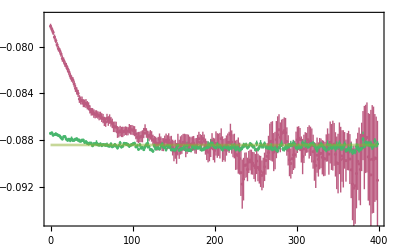

```mathematica
EMPQQbarNNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.08Evmc[[1]],.88Evmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],
Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.00510.0025

```mathematica
(Evmc-ET)/Evmc
```

0.11050.0032

```mathematica
(Egfmc-ET)/Egfmc
```

0.11500.0027

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.01120.0017

```mathematica
(ETxx-ET)/ETxx
```

0.10490.0027

### mNLO baryon

```mathematica
steps=100;
walkers=50000;
V=4/3α/(3-1)
```

0.133333

```mathematica
NCoord=3;
```

```mathematica
(*dataBase=dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

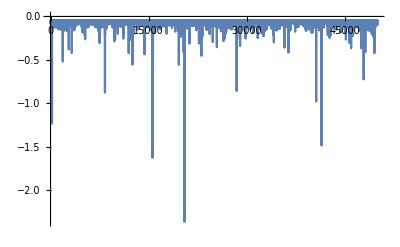

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

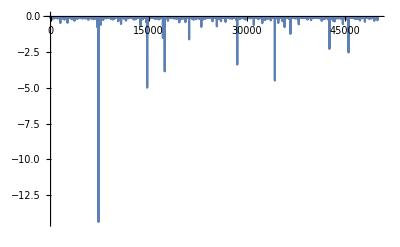

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

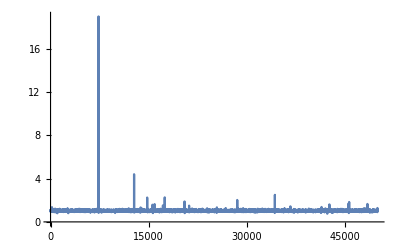

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

Import::nffil: File ~/Dropbox//physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.4_Nstep100_Nwalkers50000_Ncoord3_Nc3_Nf4_alpha0.2_spoila1_spoilfhwf.h5 not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Import::nffil: File ~/Dropbox//physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.4_Nstep100_Nwalkers50000_Ncoord3_Nc3_Nf4_alpha0.2_spoila1_spoilfhwf.h5 not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

Part::partw: Part 1 of Symbol[] does not exist.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: Symbol[]⟦1⟧ is not a list of numbers or pairs of numbers.

ListPlot[Symbol[]⟦1⟧,Joined→True,PlotRange→All]

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

Part::partw: Part 2 of Symbol[] does not exist.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: Symbol[]⟦2⟧ is not a list of numbers or pairs of numbers.

ListPlot[Symbol[]⟦2⟧,Joined→True,PlotRange→All]

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

Part::partw: Part 1 of Symbol[] does not exist.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: Symbol[]⟦1⟧ is not a list of numbers or pairs of numbers.

ListPlot[Symbol[]⟦1⟧,Joined→True,PlotRange→All]

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

Part::partw: Part 2 of Symbol[] does not exist.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: Symbol[]⟦2⟧ is not a list of numbers or pairs of numbers.

ListPlot[Symbol[]⟦2⟧,Joined→True,PlotRange→All]

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

0

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

Part::partw: Part 2 of {0} does not exist.

{0}⟦2⟧

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

25

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

50000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

RandomInteger::array: The array dimensions {200,{0}⟦2⟧} given in position 2 of RandomInteger[{1,{0}⟦2⟧},{200,{0}⟦2⟧}] should be a list of non-negative machine-sized integers giving the dimensions for the result.

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Dimensions[bootTab]
```

{0}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1,2⟧

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1,2⟧

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_ordermNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

-0.058450.00024

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,1]],Import[dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,2]]]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.4_Nstep100_Nwalkers50000_Ncoord3_Nc3_Nf4_alpha0.2_spoila1_spoilfhwf_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.4_Nstep100_Nwalkers50000_Ncoord3_Nc3_Nf4_alpha0.2_spoila1_spoilfhwf_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

$Failed⟦2,1⟧$Failed⟦2,2⟧

```mathematica
ETxx[[1]]+ETxx[[2]]
```

{}

```mathematica
EgfmcxxVec[[-1,1]]
```

Part::partw: Part -1 of {} does not exist.

{}⟦-1,1⟧

```mathematica
EMPQQbarmNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.5Egfmc[[1]],.5Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{mNLO}",Magnification->1.2]]
```

ListPlot::prng: Value of option PlotRange -> {1.5 $Failed⟦2,1⟧,0.5 $Failed⟦2,1⟧} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Part::partw: Part -1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
Export[picDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarmNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

(0.058448+$Failed⟦2,1⟧)/($Failed⟦2,1⟧)√(Abs[($Failed⟦2,2⟧)/($Failed⟦2,1⟧)^2]^2 (0.058448+$Failed⟦2,1⟧)^2+(5.67498×10^-8+($Failed⟦2,2⟧)^2)/($Failed⟦2,1⟧)^2)

```mathematica
(Evmc-ET)/Evmc
```

(-17.110.07) ((-0.058450.00024)-{}⟦1,2⟧)

```mathematica
(Egfmc-ET)/Egfmc
```

(1/($Failed⟦2,1⟧)Abs[($Failed⟦2,2⟧)/($Failed⟦2,1⟧)^2]) (($Failed⟦2,1⟧$Failed⟦2,2⟧)-{}⟦1,2⟧)

```mathematica
(Egfmc-ETxx)/Egfmc
```

(1/($Failed⟦2,1⟧)Abs[($Failed⟦2,2⟧)/($Failed⟦2,1⟧)^2]) (($Failed⟦2,1⟧$Failed⟦2,2⟧)-{}⟦1,2⟧)

```mathematica
(ETxx-ET)/ETxx
```

0

## α=0.3

```mathematica
α=0.3;
```

```mathematica
picDir=dropboxDir<>"/physics/projects/heavy_quark_nuclei/62d1dcb0570fab737342743d/figs/";
```

```mathematica
dataDir=dropboxDir<>"/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
bs=2;
```

```mathematica
dtau=0.4;
```

### LO meson

```mathematica
steps=400;
walkers=5000;
V=4/3α
```

0.4

```mathematica
NCoord=2;
```

```mathematica
(*dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

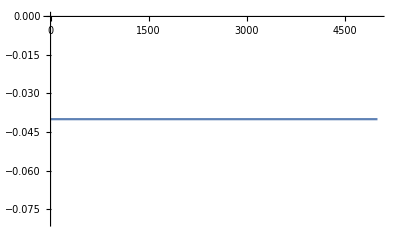

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

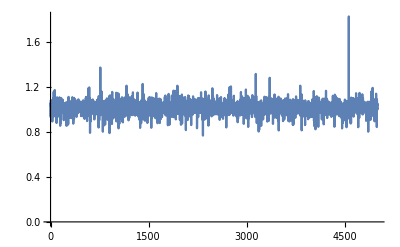

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

200

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

200

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{200,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.0399999999999999907

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.0399999999999999907

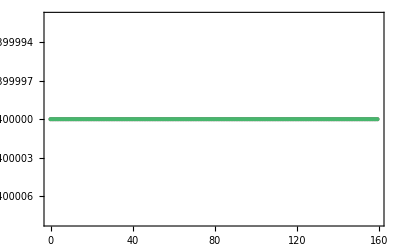

```mathematica
EMPQQbarLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}],Frame->True,PlotRange->{1.00002ET[[1]],.99998ET[[1]]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarLO];
```

### NLO meson

```mathematica
steps=400;
walkers=5000;
V=4/3α
```

0.4

```mathematica
NCoord=2;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

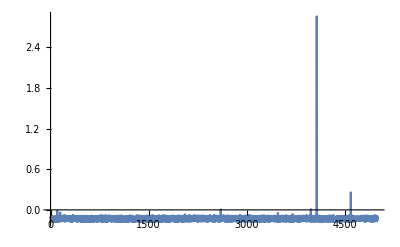

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

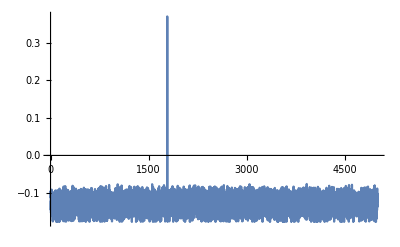

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

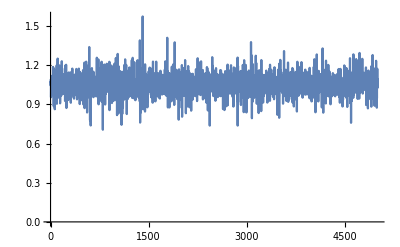

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

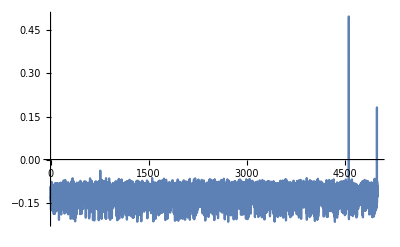

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

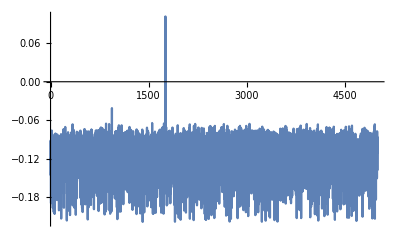

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

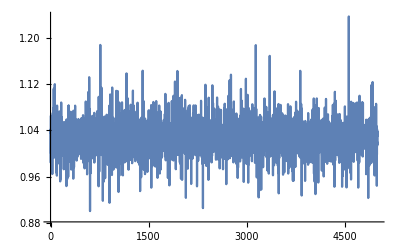

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

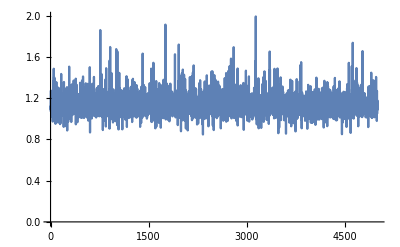

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

200

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

200

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{200,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.11890.0005

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.12410.0005

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.csv"][[2,1]],Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.csv"][[2,2]]]
```

-0.128550.00016

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.123604

```mathematica
EgfmcxxVec[[-1,1]]
```

159.2

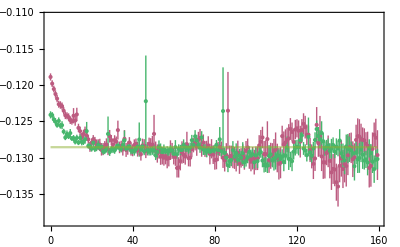

```mathematica
EMPQQbarNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.08Egfmc[[1]],.86Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNLO];
```

```mathematica
(Egfmc-ET)/Egfmc
```

0.0750.004

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.0350.004

```mathematica
(ETxx-ET)/ETxx
```

0.0420.006

### NNLO meson

```mathematica
steps=400;
walkers=5000;
V=4/3α
```

0.4

```mathematica
NCoord=2;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];.10
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

.10

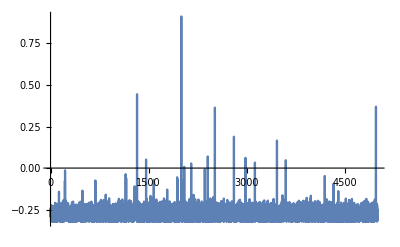

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

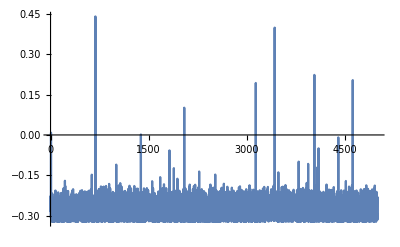

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

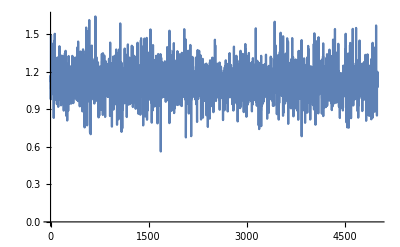

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

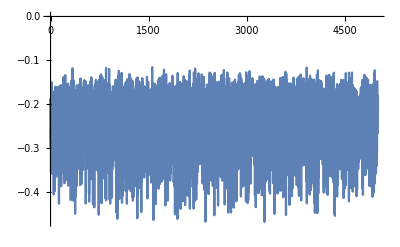

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

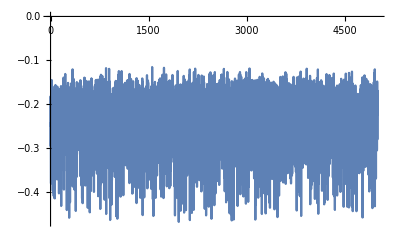

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

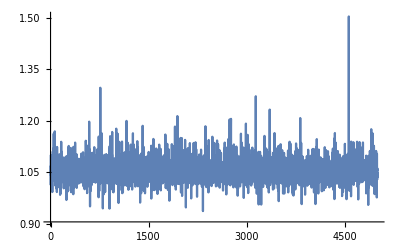

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

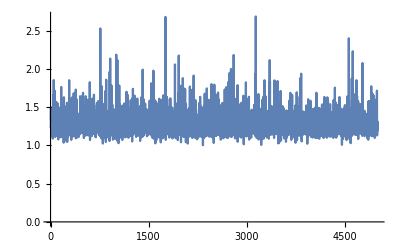

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

200

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

200

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{200,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.24130.0009

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.27170.0006

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.csv"][[2,1]],Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.csv"][[2,2]]]
```

-0.277640.00034

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.2711

```mathematica
EgfmcxxVec[[-1,1]]
```

159.2

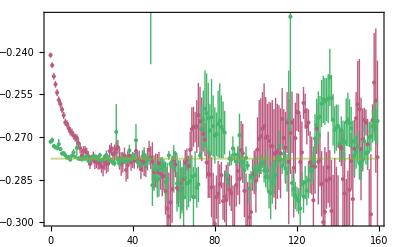

```mathematica
EMPQQbarNNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.08Egfmc[[1]],.82Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNNLO];
```

```mathematica
(Egfmc-ET)/Egfmc
```

0.13100.0034

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.02150.0024

```mathematica
(ETxx-ET)/ETxx
```

0.1120.004

### LO baryon

```mathematica
steps=400;
walkers=5000;
V=4/3α/(3-1)
```

0.2

```mathematica
NCoord=3;
```

```mathematica
(*dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r0.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r0.0.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

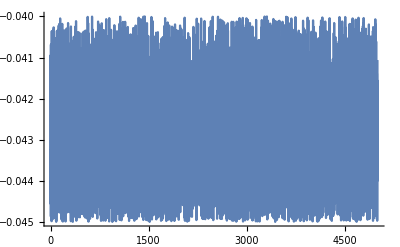

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

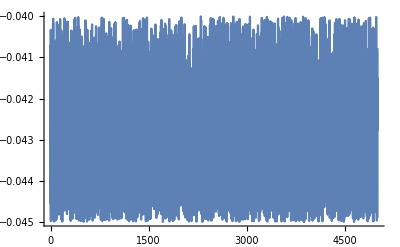

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

200

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

200

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{200,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.0428480.000019

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.0428720.000020

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,1]],Import[dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,2]]]
```

-0.0428817

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.0428522

```mathematica
EgfmcxxVec[[-1,1]]
```

159.2

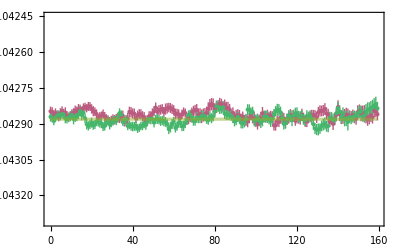

```mathematica
EMPQQbarLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.01Egfmc[[1]],.99Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

```mathematica
Export[picDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarLO];
```

```mathematica
(Egfmc-ET)/Egfmc
```

0.00080.0005

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.00020.0005

```mathematica
(ETxx-ET)/ETxx
```

0.00050.0006

### NLO baryon

```mathematica
steps=400;
walkers=5000;
V=4/3α/(3-1)
```

0.2

```mathematica
NCoord=3;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r0.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r0.0.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.5.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

200

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

200

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{200,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.13880.0004

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.153540.00021

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.5.csv"][[2,1]],Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.5.csv"][[2,2]]]
```

-0.156460.00026

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.153328

```mathematica
EgfmcxxVec[[-1,1]]
```

159.2

```mathematica
EMPQQbarNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.08Egfmc[[1]],.86Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNLO];
```

```mathematica
(Egfmc-ET)/Egfmc
```

0.11290.0031

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.01860.0022

```mathematica
(ETxx-ET)/ETxx
```

0.09610.0030

### NNLO baryon

```mathematica
steps=400;
walkers=5000;
V=4/3α/(3-1)
```

0.2

```mathematica
NCoord=3;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r0.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r0.0.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.5.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

200

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

200

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{200,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.29470.0008

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.35480.0005

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.5.csv"][[2,1]],Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.5.csv"][[2,2]]]
```

-0.358510.00016

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.354274

```mathematica
EgfmcxxVec[[-1,1]]
```

159.2

```mathematica
4/α^2
```

44.4444

```mathematica
EMPQQbarNNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.08ETxx[[1]],.82ETxx[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNNLO];
```

```mathematica
(Egfmc-ET)/Egfmc
```

0.17800.0023

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.01040.0015

```mathematica
(ETxx-ET)/ETxx
```

0.16930.0027

## α=0.4

```mathematica
α=0.4;
```

```mathematica
picDir=dropboxDir<>"/physics/projects/heavy_quark_nuclei/62d1dcb0570fab737342743d/figs/";
```

```mathematica
dataDir=dropboxDir<>"/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
bs=2;
```

```mathematica
dtau=0.4;
```

### LO meson

```mathematica
steps=250;
walkers=5000;
V=4/3α
```

0.4

```mathematica
NCoord=2;
```

```mathematica
(*dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

200

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

200

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{200,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.0399999999999999907

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.0399999999999999907

```mathematica
EMPQQbarLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}],Frame->True,PlotRange->{1.00002ET[[1]],.99998ET[[1]]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarLO];
```

### NLO meson

```mathematica
steps=250;
walkers=5000;
V=4/3α
```

0.533333

```mathematica
NCoord=2;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

125

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

125

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{125,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.25770.0009

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.28390.0018

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

Import::nffil: File ~/Dropbox (Personal)//physics/projects/heavy_quark_nuclei/data/../variational/exp1N_walkers5000p_fac10_Ncoord2_cutoff1_orderNLO_alpha0.4_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦1,1⟧,{,,[,],tensor(,+0.j}].

ToExpression::notstrbox: $Failed⟦1,1⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Import::nffil: File ~/Dropbox (Personal)//physics/projects/heavy_quark_nuclei/data/../variational/exp1N_walkers5000p_fac10_Ncoord2_cutoff1_orderNLO_alpha0.4_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦2,1⟧,{,,[,],tensor(,+0.j}].

ToExpression::notstrbox: $Failed⟦2,1⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

0.284444 $Failed0.284444 $Failed

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.0.csv"][[2,1]],Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.0.csv"][[2,2]]]
```

-0.29270.0008

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.282033

```mathematica
EgfmcxxVec[[-1,1]]
```

99.2

```mathematica
EMPQQbarNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.05Egfmc[[1]],.9Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-4.55755 (-0.219416-0.284444 $Failed)√(0.00121457 (-0.219416-0.284444 $Failed)^2+20.7713 (2.81511×10^-6+0.0809086 ($Failed)^2))

```mathematica
(Evmc-ET)/Evmc
```

(3.51563 (0.257653+0.284444 $Failed))/($Failed)√((12.3596 (8.96436×10^-7+0.0809086 ($Failed)^2))/($Failed)^2+(12.3596 (0.257653+0.284444 $Failed)^2)/Abs[$Failed]^2)

```mathematica
(Egfmc-ET)/Egfmc
```

-0.1740.009

```mathematica
(Egfmc-ETxx)/Egfmc
```

-0.2940.012

```mathematica
(ETxx-ET)/ETxx
```

0.0920.007

### NNLO meson

```mathematica
steps=250;
walkers=5000;
V=4/3α
```

0.533333

```mathematica
NCoord=2;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];.10
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

.10

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

125

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

125

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{125,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.64630.0025

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.7360.008

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

Import::nffil: File ~/Dropbox (Personal)//physics/projects/heavy_quark_nuclei/data/../variational/exp1N_walkers5000p_fac10_Ncoord2_cutoff1_orderNNLO_alpha0.4_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦1,1⟧,{,,[,],tensor(,+0.j}].

ToExpression::notstrbox: $Failed⟦1,1⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Import::nffil: File ~/Dropbox (Personal)//physics/projects/heavy_quark_nuclei/data/../variational/exp1N_walkers5000p_fac10_Ncoord2_cutoff1_orderNNLO_alpha0.4_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦2,1⟧,{,,[,],tensor(,+0.j}].

ToExpression::notstrbox: $Failed⟦2,1⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

0.284444 $Failed0.284444 $Failed

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.0.csv"][[2,1]],Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.0.csv"][[2,2]]]
```

-0.9410.016

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.727956

```mathematica
EgfmcxxVec[[-1,1]]
```

99.2

```mathematica
EMPQQbarNNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.08Egfmc[[1]],.5Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-1.06214 (-0.941498-0.284444 $Failed)√(0.000309114 (-0.941498-0.284444 $Failed)^2+1.12814 (0.000242882+0.0809086 ($Failed)^2))

```mathematica
(Evmc-ET)/Evmc
```

(3.51563 (0.646281+0.284444 $Failed))/($Failed)√((12.3596 (6.48971×10^-6+0.0809086 ($Failed)^2))/($Failed)^2+(12.3596 (0.646281+0.284444 $Failed)^2)/Abs[$Failed]^2)

```mathematica
(Egfmc-ET)/Egfmc
```

0.3140.018

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.2180.019

```mathematica
(ETxx-ET)/ETxx
```

0.1220.011

### LO baryon

```mathematica
steps=400;
walkers=5000;
V=4/3α/(3-1)
```

0.2

```mathematica
NCoord=3;
```

```mathematica
(*dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r0.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r0.0.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

200

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

200

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{200,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.0428720.000019

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.0428720.000020

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

Import::nffil: File ~/Dropbox//physics/projects/heavy_quark_nuclei/data/../variational/exp1N_walkers5000p_fac10_Ncoord3_cutoff1_orderLO_alpha0.3_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦1,1⟧,{,,[,],tensor(,+0.j}].

ToExpression::notstrbox: $Failed⟦1,1⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Import::nffil: File ~/Dropbox//physics/projects/heavy_quark_nuclei/data/../variational/exp1N_walkers5000p_fac10_Ncoord3_cutoff1_orderLO_alpha0.3_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦2,1⟧,{,,[,],tensor(,+0.j}].

ToExpression::notstrbox: $Failed⟦2,1⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

0.04 $Failed0.04 $Failed

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,1]],Import[dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,2]]]
```

-0.0428817

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.0428521

```mathematica
EgfmcxxVec[[-1,1]]
```

159.2

```mathematica
EMPQQbarLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.01Egfmc[[1]],.99Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-23.3201 (-0.0428815-0.04 $Failed)√(0.0000128439 (-0.0428815-0.04 $Failed)^2+543.827 (4.34284×10^-11+0.0016 ($Failed)^2))

```mathematica
(Evmc-ET)/Evmc
```

(25. (0.0428719+0.04 $Failed))/($Failed)√((625. (3.68802×10^-10+0.0016 ($Failed)^2))/($Failed)^2+(625. (0.0428719+0.04 $Failed)^2)/Abs[$Failed]^2)

```mathematica
(Egfmc-ET)/Egfmc
```

0.00020.0005

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.00020.0005

```mathematica
(ETxx-ET)/ETxx
```

0.00000.0006

### NLO baryon

```mathematica
steps=400;
walkers=5000;
V=4/3α/(3-1)
```

0.2

```mathematica
NCoord=3;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r0.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r0.0.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

200

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

200

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{200,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.124920.00034

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.130620.00027

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

Import::nffil: File ~/Dropbox//physics/projects/heavy_quark_nuclei/data/../variational/exp1N_walkers5000p_fac10_Ncoord3_cutoff1_orderNLO_alpha0.3_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦1,1⟧,{,,[,],tensor(,+0.j}].

ToExpression::notstrbox: $Failed⟦1,1⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Import::nffil: File ~/Dropbox//physics/projects/heavy_quark_nuclei/data/../variational/exp1N_walkers5000p_fac10_Ncoord3_cutoff1_orderNLO_alpha0.3_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦2,1⟧,{,,[,],tensor(,+0.j}].

ToExpression::notstrbox: $Failed⟦2,1⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

0.04 $Failed0.04 $Failed

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,1]],Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,2]]]
```

-0.135840.00012

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.130352

```mathematica
EgfmcxxVec[[-1,1]]
```

159.2

```mathematica
EMPQQbarNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.05Egfmc[[1]],.9Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-7.36144 (-0.135843-0.04 $Failed)√(0.0000456363 (-0.135843-0.04 $Failed)^2+54.1908 (1.55403×10^-8+0.0016 ($Failed)^2))

```mathematica
(Evmc-ET)/Evmc
```

(25. (0.124918+0.04 $Failed))/($Failed)√((625. (1.17726×10^-7+0.0016 ($Failed)^2))/($Failed)^2+(625. (0.124918+0.04 $Failed)^2)/Abs[$Failed]^2)

```mathematica
(Egfmc-ET)/Egfmc
```

0.08040.0027

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.03840.0022

```mathematica
(ETxx-ET)/ETxx
```

0.04370.0033

### NNLO baryon

```mathematica
steps=400;
walkers=5000;
V=4/3α/(3-1)
```

0.2

```mathematica
NCoord=3;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r0.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r0.0.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r0.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

100

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

100

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{100,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.25050.0007

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.27850.0014

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/../variational/exp1N_walkers5000p_fac10_Ncoord3_cutoff1_orderNNLO_alpha0.3_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦1,1⟧,{,,[,],tensor(,+0.j}].

ToExpression::notstrbox: $Failed⟦1,1⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/../variational/exp1N_walkers5000p_fac10_Ncoord3_cutoff1_orderNNLO_alpha0.3_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed⟦2,1⟧,{,,[,],tensor(,+0.j}].

ToExpression::notstrbox: $Failed⟦2,1⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

0.04 $Failed0.04 $Failed

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,1]],Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,2]]]
```

-0.28890.0011

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.277112

```mathematica
EgfmcxxVec[[-1,1]]
```

158.4

```mathematica
4/α^2
```

44.4444

```mathematica
EMPQQbarNNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.08Egfmc[[1]],.85Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-3.46179 (-0.288868-0.04 $Failed)√(0.000160533 (-0.288868-0.04 $Failed)^2+11.984 (1.1178×10^-6+0.0016 ($Failed)^2))

```mathematica
(Evmc-ET)/Evmc
```

(25. (0.250498+0.04 $Failed))/($Failed)√((625. (4.81056×10^-7+0.0016 ($Failed)^2))/($Failed)^2+(625. (0.250498+0.04 $Failed)^2)/Abs[$Failed]^2)

```mathematica
(Egfmc-ET)/Egfmc
```

0.1330.004

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.0360.006

```mathematica
(ETxx-ET)/ETxx
```

0.1010.006

## α=0.6

```mathematica
α=0.6;
```

```mathematica
picDir=dropboxDir<>"/physics/projects/heavy_quark_nuclei/62d1dcb0570fab737342743d/figs/";
```

```mathematica
dataDir=dropboxDir<>"/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
bs=2;
```

```mathematica
dtau=0.4;
```

### LO meson

```mathematica
steps=200;
walkers=5000;
V=4/3α
```

0.8

```mathematica
NCoord=2;
```

```mathematica
(*dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

201

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

201

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

Get::noopen: Cannot open CloudObjectLoader`.

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{201,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.16

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.16

```mathematica
EMPQQbarLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.05ET,.9ET},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EMPQQbarLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}],Frame->True,PlotRange->{1.00002ET,.99998ET}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarLO];
```

### NLO meson

```mathematica
steps=200;
walkers=5000;
V=4/3α
```

0.8

```mathematica
NCoord=2;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.0.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
Mean[gfmcxxHammys[[1]]]
```

-0.882871

```mathematica
Mean[gfmcHammys[[1]]]
```

-0.78583

```mathematica
dataBase
```

~/Dropbox (Personal)//physics/projects/heavy_quark_nuclei/data/Hammys_NLO_dtau0.4_Nstep200_Nwalkers5000_Ncoord2_Nc3_Nf4_alpha0.6_spoila1_spoilfhwf_log_mu_r1.0.h5

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

100

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

100

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{100,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.8020.004

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.9090.008

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

-0.9070.009

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.0.csv"][[2,1]],Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.0.csv"][[2,2]]]
```

-0.9920.009

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.901208

```mathematica
EgfmcxxVec[[-1,1]]
```

79.2

```mathematica
EMPQQbarNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.05Egfmc[[1]],.9Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EMPQQbarNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.5Egfmc[[1]],.5Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNLO];
```

Export::nodir: Directory /Users/mwagman/Dropbox/physics/projects/heavy_quark_nuclei/62d1dcb0570fab737342743d/figs/ does not exist.

Export::noopen: Cannot open ~/Dropbox//physics/projects/heavy_quark_nuclei/62d1dcb0570fab737342743d/figs/Hammys_NLO_dtau0.4_Nstep200_Nwalkers5000_Ncoord2_Nc3_Nf4_alpha0.6_EMP.pdf.

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.0860.013

```mathematica
(Evmc-ET)/Evmc
```

0.1160.011

```mathematica
(Egfmc-ET)/Egfmc
```

0.1920.010

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.0840.012

```mathematica
(ETxx-ET)/ETxx
```

0.1180.009

### NNLO meson

```mathematica
steps=200;
walkers=5000;
V=4/3α
```

0.8

```mathematica
NCoord=2;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

201

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

201

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{201,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-1.5120.004

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

0.000.05

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

-2.610.06

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,1]],Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,2]]]
```

-3.670.11

```mathematica
ETxx[[1]]+ETxx[[2]]
```

0.060466

```mathematica
EgfmcxxVec[[-1,1]]
```

80.

```mathematica
EMPQQbarNNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.5Evmc[[1]],.5Evmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.2890.034

```mathematica
(Evmc-ET)/Evmc
```

0.4210.023

```mathematica
(Egfmc-ET)/Egfmc
```

0.5880.034

```mathematica
(Egfmc-ETxx)/Egfmc
```

1.000.04

```mathematica
(ETxx-ET)/ETxx
```

0.21.310^3

### mNLO meson

```mathematica
steps=100;
walkers=50000;
V=4/3α
```

0.266667

```mathematica
NCoord=2;
```

```mathematica
dataBase=dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcxxHammys[[1,1]]
```

-0.0496125

```mathematica
gfmcxxHammys[[1,1]]
```

-0.0496125

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

101

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

50000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

101

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

50000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
ListPlot[bootTab[[1]],Joined->True]
```

-Graphics-

```mathematica
ListPlot[xxbootTab[[1]],Joined->True]
```

-Graphics-

```mathematica
Dimensions[bootTab]
```

{101,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.046460.00017

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.053180.00021

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_ordermNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

-0.052490.00028

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,1]],Import[dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,2]]]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.4_Nstep100_Nwalkers50000_Ncoord2_Nc3_Nf4_alpha0.2_spoila1_spoilfhwf_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.4_Nstep100_Nwalkers50000_Ncoord2_Nc3_Nf4_alpha0.2_spoila1_spoilfhwf_log_mu_r1.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

$Failed⟦2,1⟧$Failed⟦2,2⟧

```mathematica
EMPQQbarmNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{{0,40},{2Evmc[[1]],.0Evmc[[1]]}},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q"]},PlotLabel->MaTeX["\\text{mNLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarmNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-0.1110.007

```mathematica
(Evmc-ET)/Evmc
```

0.1160.009

```mathematica
(Egfmc-ET)/Egfmc
```

0.0180.009

```mathematica
(Egfmc-ETxx)/Egfmc
```

-0.180.04

```mathematica
(ETxx-ET)/ETxx
```

0.160.04

### LO baryon

```mathematica
steps=200;
walkers=5000;
V=4/3α/(3-1)
```

0.4

```mathematica
NCoord=3;
```

```mathematica
(*dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

201

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

201

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{201,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.171550.00009

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.171550.00008

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

-0.171360.00008

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,1]],Import[dataDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,2]]]
```

-0.1714470.000029

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.171468

```mathematica
EgfmcxxVec[[-1,1]]
```

80.

```mathematica
EMPQQbarLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.05Egfmc[[1]],.9Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EMPQQbarLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.01Egfmc[[1]],.99Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.00050.0005

```mathematica
(Evmc-ET)/Evmc
```

-0.00110.0007

```mathematica
(Egfmc-ET)/Egfmc
```

-0.00060.0005

```mathematica
(Egfmc-ETxx)/Egfmc
```

-0.00060.0005

```mathematica
(ETxx-ET)/ETxx
```

0.00000.0007

### NLO baryon

```mathematica
steps=200;
walkers=5000;
V=4/3α/(3-1)
```

0.4

```mathematica
NCoord=3;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

201

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

201

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{201,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.64060.0018

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.5330.012

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

-1.1380.012

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,1]],Import[dataDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,2]]]
```

-0.7240.010

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.521786

```mathematica
EgfmcxxVec[[-1,1]]
```

80.

```mathematica
EMPQQbarNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.55ET[[1]],.5ET[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

-0.5710.023

```mathematica
(Evmc-ET)/Evmc
```

0.4370.011

```mathematica
(Egfmc-ET)/Egfmc
```

0.1160.015

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.2640.022

```mathematica
(ETxx-ET)/ETxx
```

-0.2010.022

### NNLO baryon

```mathematica
steps=1000;
walkers=5000;
V=4/3α/(3-1)
```

0.133333

```mathematica
NCoord=3;
```

```mathematica
(*dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

250

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

250

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{250,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.078240.00019

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.088270.00016

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_orderNNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

-0.087960.00019

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,1]],Import[dataDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,2]]]
```

-0.088700.00007

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.0881165

```mathematica
EgfmcxxVec[[-1,1]]
```

398.4

```mathematica
4/α^2
```

100.

```mathematica
EMPQQbarNNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.08Evmc[[1]],.88Evmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Graphics[{ColorData[97][3],Opacity[0.5],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],
```

```mathematica
Export[picDir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarNNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.00830.0022

```mathematica
(Evmc-ET)/Evmc
```

0.11050.0031

```mathematica
(Egfmc-ET)/Egfmc
```

0.11790.0023

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.00480.0019

```mathematica
(ETxx-ET)/ETxx
```

0.11360.0028

### mNLO baryon

```mathematica
steps=1000;
walkers=5000;
V=4/3α/(3-1)
```

0.133333

```mathematica
NCoord=3;
```

```mathematica
(*dataBase=dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_1_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
Do[
gfmcxxHammys2=gfmcxxHammys;
gfmcxxWs2=gfmcxxWs;
dataBase=dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwfround_"<>ToString[r]<>"_log_mu_r1.h5";
gfmcxxHammys=Transpose[Join[Transpose[gfmcxxHammys2],Transpose[Import[dataBase,{"Datasets","Hammys"}][[All,All,1]]]]];
gfmcxxWs=Transpose[Join[Transpose[gfmcxxWs2],Transpose[Import[dataBase,{"Datasets","Ws"}][[All,All,1]]]]];
,{r,2,4}];*)
```

```mathematica
dataBase=dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.h5";
gfmcxxHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcxxWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcxxHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcxxWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcxxHammysUB=gfmcxxHammys;
gfmcxxWsUB=gfmcxxWs;
```

```mathematica
gfmcxxHammys=Bin[gfmcxxHammysUB,bs];
gfmcxxWs=Bin[gfmcxxWsUB,bs];
```

```mathematica
dataBase=dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf.h5";
gfmcHammys=Import[dataBase,{"Datasets","Hammys"}][[All,All,1]];
gfmcWs=Import[dataBase,{"Datasets","Ws"}][[All,All,1]];
```

```mathematica
ListPlot[gfmcHammys[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcHammys[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[1]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[gfmcWs[[2]],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
gfmcHammysUB=gfmcHammys;
gfmcWsUB=gfmcWs;
```

```mathematica
gfmcHammys=Bin[gfmcHammysUB,bs];
gfmcWs=Bin[gfmcWsUB,bs];
```

```mathematica
Lt=Dimensions[gfmcHammys][[1]]
```

250

```mathematica
Nmeas=Dimensions[gfmcHammys][[2]]
```

5000

```mathematica
xxLt=Dimensions[gfmcxxHammys][[1]]
```

250

```mathematica
xxNmeas=Dimensions[gfmcxxHammys][[2]]
```

5000

```mathematica
bootIndices=RandomInteger[{1,Nmeas},{Nboot,Nmeas}];
```

```mathematica
xxbootIndices=RandomInteger[{1,xxNmeas},{Nboot,xxNmeas}];
```

```mathematica
Nboot=200;
```

```mathematica
bootTab=ParallelTable[Table[Mean[gfmcHammys[[t,bootIndices[[b]]]]gfmcWs[[t,bootIndices[[b]]]]]/Mean[gfmcWs[[t,bootIndices[[b]]]]],{b,1,Nboot}],{t,Lt}];
```

```mathematica
xxbootTab=ParallelTable[Table[Mean[gfmcxxHammys[[t,xxbootIndices[[b]]]]gfmcxxWs[[t,xxbootIndices[[b]]]]]/Mean[gfmcxxWs[[t,xxbootIndices[[b]]]]],{b,1,Nboot}],{t,xxLt}];
```

```mathematica
Dimensions[bootTab]
```

{250,200}

```mathematica
EgfmcVec=Table[{dtau bs (t-1),Around[Mean[gfmcHammys[[t]]gfmcWs[[t]]]/Mean[gfmcWs[[t]]],CI[bootTab[[t]]]]},{t,Lt}];
```

```mathematica
EgfmcxxVec=Table[{dtau bs (t-1),Around[Mean[gfmcxxHammys[[t]]gfmcxxWs[[t]]]/Mean[gfmcxxWs[[t]]],CI[xxbootTab[[t]]]]},{t,xxLt}];
```

```mathematica
ET=EgfmcVec[[1,2]]
```

-0.05180.0004

```mathematica
ETxx=EgfmcxxVec[[1,2]]
```

-0.058510.00027

```mathematica
crazyFormat[file_]:=Around[((Import[dataDir<>"../variational"<>file][[1,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x,((Import[dataDir<>"../variational"<>file][[2,1]]//StringSplit[#,{",","[","]","tensor(","+0.j"}]&)[[1]]//ToExpression)/. x_+y_*e:>y*10^x]
```

```mathematica
Evmc=V^2 crazyFormat["/exp1N_walkers5000p_fac10_Ncoord"<>ToString[NCoord]<>"_cutoff1_ordermNLO_alpha"<>ToString[α]<>"_log_mu_r1.csv"]
```

-0.058450.00024

```mathematica
Egfmc=Around[Import[dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,1]],Import[dataDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_spoila1_spoilfhwf_log_mu_r1.csv"][[2,2]]]
```

-0.057590.00025

```mathematica
ETxx[[1]]+ETxx[[2]]
```

-0.0582368

```mathematica
EgfmcxxVec[[-1,1]]
```

398.4

```mathematica
EMPQQbarmNLO=Show[ListPlot[{EgfmcVec,EgfmcxxVec},PlotStyle->{ColorData[97][14],ColorData[97][15]},IntervalMarkersStyle->{ColorData[97][14],ColorData[97][15]},Frame->True,PlotRange->{1.5Egfmc[[1]],.5Egfmc[[1]]},PlotLegends->Placed[gfmcLegend,{0.5,0.9}]],Graphics[{ColorData[97][1],Opacity[0],Rectangle[{0,ETxx[[1]]-ETxx[[2]]},{EgfmcVec[[-1,1]],ETxx[[1]]+ETxx[[2]]}]}],Graphics[{ColorData[97][17],Opacity[0],Rectangle[{0,Evmc[[1]]-Evmc[[2]]},{EgfmcVec[[-1,1]],Evmc[[1]]+Evmc[[2]]}]}],Graphics[{ColorData[97][3],Opacity[0],Rectangle[{0,Egfmc[[1]]-Egfmc[[2]]},{EgfmcVec[[-1,1]],Egfmc[[1]]+Egfmc[[2]]}]}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau\, m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]},PlotLabel->MaTeX["\\text{mNLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Export[picDir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[steps]<>"_Nwalkers"<>ToString[walkers]<>"_Ncoord"<>ToString[NCoord]<>"_Nc3_Nf4_alpha"<>ToString[α]<>"_EMP.pdf",EMPQQbarmNLO];
```

```mathematica
(Egfmc-Evmc)/Egfmc
```

0.0020.029

```mathematica
(Evmc-ET)/Evmc
```

(-17.110.07) ((-0.058450.00024)-{}⟦1,2⟧)

```mathematica
(Egfmc-ET)/Egfmc
```

(-17.10.5) ((-0.05860.0017)-{}⟦1,2⟧)

```mathematica
(Egfmc-ETxx)/Egfmc
```

0.0010.029

```mathematica
(ETxx-ET)/ETxx
```

(-17.090.07) ((-0.058510.00024)-{}⟦1,2⟧)